```mathematica
Needs["PlotLegends`"]
```

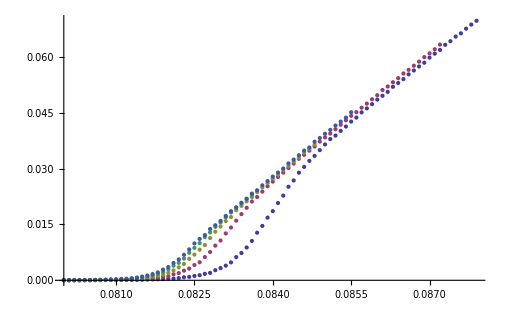

```mathematica
n=3;
g10k=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/v9/v9-10k.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
g20k=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/v9/v9-20k.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
g30k=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/v9/v9-30k.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
g40k=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/v9/v9-40k.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
g50k=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/v9/v9-50k.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
gap10v9=Table[{g10k[[All,1]][[j]],Sum[g10k[[All,i]][[j]],{i,2,n+2}]},{j,1,Length[g10k]}];
gap20v9=Table[{g20k[[All,1]][[j]],Sum[g20k[[All,i]][[j]],{i,2,n+2}]},{j,1,Length[g20k]}];
gap30v9=Table[{g30k[[All,1]][[j]],Sum[g30k[[All,i]][[j]],{i,2,n+2}]},{j,1,Length[g30k]}];
gap40v9=Table[{g40k[[All,1]][[j]],Sum[g40k[[All,i]][[j]],{i,2,n+2}]},{j,1,Length[g40k]}];
gap50v9=Table[{g50k[[All,1]][[j]],Sum[g50k[[All,i]][[j]],{i,2,n+2}]},{j,1,Length[g50k]}];
ListPlot[{gap10v9,gap20v9,gap30v9,gap40v9,gap50v9}]


ga10k1=gap10v9[[All,1]];
ga20k1=gap20v9[[All,1]];
ga30k1=gap30v9[[All,1]];
ga40k1=gap40v9[[All,1]];
ga50k1=gap50v9[[All,1]];

ga10k2=gap10v9[[All,2]];
ga20k2=gap20v9[[All,2]];
ga30k2=gap30v9[[All,2]];
ga40k2=gap40v9[[All,2]];
ga50k2=gap50v9[[All,2]];
```

0.0751

0.1

0.25

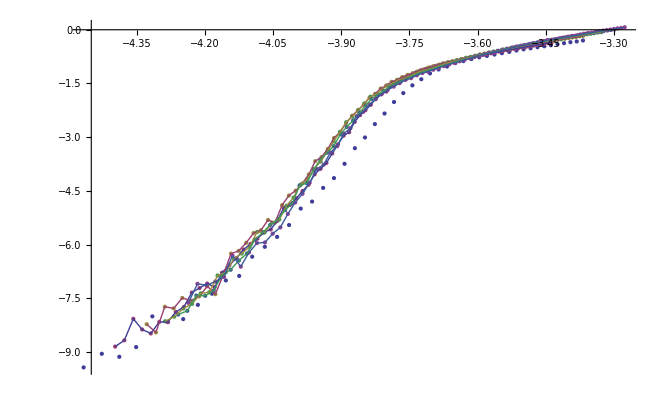

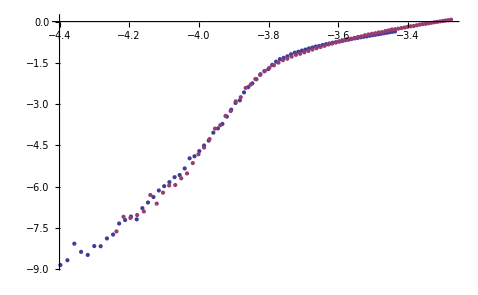

```mathematica
ClearAll[d0,z,α];
d0=0.0751;
z=0.1;
α=0.25;

ga5k1=gap5v9[[All,1]];
ga10k1=gap10v9[[All,1]];
ga20k1=gap20v9[[All,1]];
ga30k1=gap30v9[[All,1]];
ga40k1=gap40v9[[All,1]];
ga50k1=gap50v9[[All,1]];

ga5k2=gap5v9[[All,2]];
ga10k2=gap10v9[[All,2]];
ga20k2=gap20v9[[All,2]];
ga30k2=gap30v9[[All,2]];
ga40k2=gap40v9[[All,2]];
ga50k2=gap50v9[[All,2]];

g5k=Table[{Log[ga5k1[[i]]-d0]+z*Log[5*1000.],
Log[ga5k2[[i]]]+α*Log[5*1000.]},{i,1,Length[ga5k1]}];
g10k=Table[{Log[ga10k1[[i]]-d0]+z*Log[10*1000.],
Log[ga10k2[[i]]]+α*Log[10*1000.]},{i,1,Length[ga10k1]}];

g20k=Table[{Log[ga20k1[[i]]-d0]+z*Log[20*1000.],Log[ga20k2[[i]]]+α*Log[20*1000.]},{i,1,Length[ga20k1]}];
g30k=Table[{Log[ga30k1[[i]]-d0]+z*Log[30*1000.],Log[ga30k2[[i]]]+α*Log[30*1000.]},{i,1,Length[ga30k1]}];
g40k=Table[{Log[ga40k1[[i]]-d0]+z*Log[40*1000.],Log[ga40k2[[i]]]+α*Log[40*1000.]},{i,1,Length[ga40k1]}];
g50k=Table[{Log[ga50k1[[i]]-d0]+z*Log[50*1000.],Log[ga50k2[[i]]]+α*Log[50*1000.]},{i,1,Length[ga50k1]}];
pic5=ListPlot[{g5k,g10k,g20k,g30k,g40k,g50k},PlotRange->Full];
pic6=ListLinePlot[{g10k,g20k,g30k,g40k,g50k},PlotRange->Full];
d0
z
α
Show[{pic5,pic6}]
ListPlot[{g10k,g50k}]
```

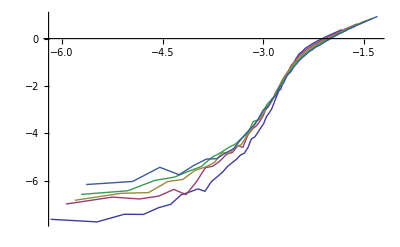

```mathematica
ListPlot[{g10k,g20k,g30k,g40k,g50k},PlotLegend->{"5k","10k","20k","30k","40k","50k"},LegendPosition->{1.1,-0.4},LegendShadow->None,Joined->{True}]
```

```mathematica
gap1000=Table[{g100k1[[All,1]][[j]],Sum[g100k1[[All,i]][[j]],{i,2,2}]},{j,1,Length[g100k1]}];
gap1001=Table[{g100k1[[All,1]][[j]],Sum[g100k1[[All,i]][[j]],{i,3,3}]},{j,1,Length[g100k1]}];
gap1002=Table[{g100k1[[All,1]][[j]],Sum[g100k1[[All,i]][[j]],{i,4,4}]},{j,1,Length[g100k1]}];
gap1003=Table[{g100k1[[All,1]][[j]],Sum[g100k1[[All,i]][[j]],{i,5,5}]},{j,1,Length[g100k1]}];
gap1004=Table[{g100k1[[All,1]][[j]],Sum[g100k1[[All,i]][[j]],{i,6,6}]},{j,1,Length[g100k1]}];
gap1005=Table[{g100k1[[All,1]][[j]],Sum[g100k1[[All,i]][[j]],{i,7,7}]},{j,1,Length[g100k1]}];
gap1006=Table[{g100k1[[All,1]][[j]],Sum[g100k1[[All,i]][[j]],{i,8,8}]},{j,1,Length[g100k1]}];
gap1007=Table[{g100k1[[All,1]][[j]],Sum[g100k1[[All,i]][[j]],{i,9,9}]},{j,1,Length[g100k1]}];
gap1008=Table[{g100k1[[All,1]][[j]],Sum[g100k1[[All,i]][[j]],{i,10,10}]},{j,1,Length[g100k1]}];
```

```mathematica
gapa1000=Table[{g100k1[[All,1]][[j]],Sum[g100k1[[All,i]][[j]],{i,2,2}]},{j,1,Length[g100k1]}];
gapa1001=Table[{g100k1[[All,1]][[j]],Sum[g100k1[[All,i]][[j]],{i,2,3}]},{j,1,Length[g100k1]}];
gapa1002=Table[{g100k1[[All,1]][[j]],Sum[g100k1[[All,i]][[j]],{i,2,4}]},{j,1,Length[g100k1]}];
gapa1003=Table[{g100k1[[All,1]][[j]],Sum[g100k1[[All,i]][[j]],{i,2,5}]},{j,1,Length[g100k1]}];
gapa1004=Table[{g100k1[[All,1]][[j]],Sum[g100k1[[All,i]][[j]],{i,2,6}]},{j,1,Length[g100k1]}];
gapa1005=Table[{g100k1[[All,1]][[j]],Sum[g100k1[[All,i]][[j]],{i,2,7}]},{j,1,Length[g100k1]}];
gapa1006=Table[{g100k1[[All,1]][[j]],Sum[g100k1[[All,i]][[j]],{i,2,8}]},{j,1,Length[g100k1]}];
gapa1007=Table[{g100k1[[All,1]][[j]],Sum[g100k1[[All,i]][[j]],{i,2,9}]},{j,1,Length[g100k1]}];
gapa1008=Table[{g100k1[[All,1]][[j]],Sum[g100k1[[All,i]][[j]],{i,2,10}]},{j,1,Length[g100k1]}];
```

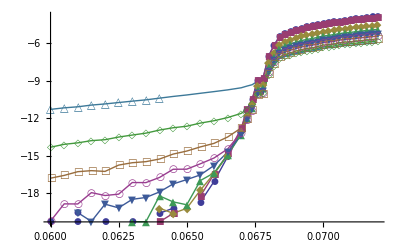

```mathematica
ListLogPlot[{gap1000,gap1001,gap1002,gap1003,gap1004,gap1005,gap1006,gap1007,gap1008},PlotLegend->{"0","1","2","3","4","5","6","7","8"},LegendPosition->{1.1,-0.4},LegendShadow->None,Joined->{True},PlotMarkers->Automatic,PlotRange->Full]
```

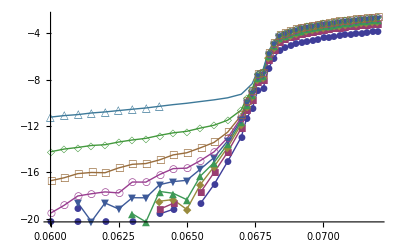

```mathematica
ListLogPlot[{gapa1000,gapa1001,gapa1002,gapa1003,gapa1004,gapa1005,gapa1006,gapa1007,gapa1008},PlotLegend->{"0","1","2","3","4","5","6","7","8"},LegendPosition->{1.1,-0.4},LegendShadow->None,Joined->{True},PlotMarkers->Automatic,PlotRange->Full]
```

```mathematica
Log[2.7181]
```

0.999933